```mathematica
SphericalHarmonicY[1,-1,θ,ϕ]
```

1/2 ⅇ^(-ⅈ ϕ) √(3/(2 π)) Sin[θ]

```mathematica
SphericalHarmonicY[1,0,θ,ϕ]
```

1/2 √(3/π) Cos[θ]

```mathematica
SphericalHarmonicY[1,1,θ,ϕ]
```

-1/2 ⅇ^(ⅈ ϕ) √(3/(2 π)) Sin[θ]

```mathematica
ex={1,0,0};ey={0,1,0};ez={0,0,1};
```

```mathematica
ep=-(ex+I*ey)/Sqrt[2];em=+(ex-I*ey)/Sqrt[2];
```

```mathematica
c1Star[m_]:=Conjugate[Sqrt[4Pi/3]*SphericalHarmonicY[1,m,θ,ϕ]];
```

```mathematica
FullSimplify[c1Star[-1]*em+c1Star[+1]*ep+c1Star[0]*ez,Assumptions->{ϕ>0,θ>0}]
```

{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}

```mathematica
(*Extra credit*)
```

```mathematica
(*Hamiltonian matrix elements*)
```

```mathematica
H[J_,JJ_,mJ_,mJJ_]:=B*J*(J+1)*KroneckerDelta[J,JJ]*KroneckerDelta[mJ,mJJ]-d*e*(-1)^(-mJJ)*Sqrt[(2J+1)*(2*1+1)*(2*JJ+1)/3]*ThreeJSymbol[{J,0},{1,0},{JJ,0}]*ThreeJSymbol[{J,mJ},{1,0},{JJ,-mJJ}];
```

```mathematica
Jmax=3;
```

```mathematica
Basis=Flatten[Table[{J,mJ},{J,0,Jmax},{mJ,-J,J}],1];
```

```mathematica
HMatrix[r_,c_]:=H[Basis[[c]][[1]],Basis[[r]][[1]],Basis[[c]][[2]],Basis[[r]][[2]]];
```

```mathematica
HMat=Table[HMatrix[r,c],{r,1,(Jmax+1)^2},{c,1,(Jmax+1)^2}];
```

ClebschGordan::tri: ThreeJSymbol[{0,0},{1,0},{0,0}] is not triangular.

ClebschGordan::phy: ThreeJSymbol[{1,-1},{1,0},{0,0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1,1},{1,0},{0,0}] is not physical.

ClebschGordan::tri: ThreeJSymbol[{2,0},{1,0},{0,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{0,0},{1,0},{1,1}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

```mathematica
(*Setting dE/B=0*)
```

```mathematica
HMat/B/.{d*e/B->0}//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12)

```mathematica
Eigenvalues[HMat/B/.{d*e/B->0}]//FullSimplify
```

{12,12,12,12,12,12,12,6,6,6,6,6,2,2,2,0}

```mathematica
HMat/B/.{d*e/B->1}//MatrixForm
```

(0 | 0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | -1/(√5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/(√3) | 0 | 2 | 0 | 0 | 0 | -2/(√15) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0 | -1/(√5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | -1/(√7) | 0 | 0 | 0 | 0 | 0
0 | -1/(√5) | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | -2 √(2/35) | 0 | 0 | 0 | 0
0 | 0 | -2/(√15) | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | -3/(√35) | 0 | 0 | 0
0 | 0 | 0 | -1/(√5) | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | -2 √(2/35) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | -1/(√7) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/(√7) | 0 | 0 | 0 | 0 | 0 | 12 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -2 √(2/35) | 0 | 0 | 0 | 0 | 0 | 12 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -3/(√35) | 0 | 0 | 0 | 0 | 0 | 12 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 √(2/35) | 0 | 0 | 0 | 0 | 0 | 12 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√7) | 0 | 0 | 0 | 0 | 0 | 12 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12)

```mathematica
(*The rest is done in MATLAB*)
```

```mathematica
(*Will only use mathematica to plot stuff*)
```

```mathematica
(*I will input results from MATLAB*)
```

```mathematica
(*test basis ordering*)
```

```mathematica
Jmax0=4;
```

```mathematica
Basis0=Flatten[Table[{J,mJ},{J,0,Jmax0},{mJ,-J,J}],1];
```

```mathematica
Basis0
```

{{0,0},{1,-1},{1,0},{1,1},{2,-2},{2,-1},{2,0},{2,1},{2,2},{3,-3},{3,-2},{3,-1},{3,0},{3,1},{3,2},{3,3},{4,-4},{4,-3},{4,-2},{4,-1},{4,0},{4,1},{4,2},{4,3},{4,4}}

```mathematica
(*dE/B=0 ---> |0,0> state*)
```

```mathematica
Energy1=0;
```

```mathematica
State1=SphericalHarmonicY[0,0,θ,ϕ];
```

```mathematica
SphericalPlot3D[Conjugate[State1]*State1,{θ,0,Pi},{ϕ,0,2Pi},PlotRange->All]
```

-Graphics3D-

```mathematica
(*dE/B=1 ---> get superposition state*)
```

```mathematica
Jmax2=4;
```

```mathematica
Base2=Flatten[Table[SphericalHarmonicY[J,mJ,θ,ϕ],{J,0,Jmax2},{mJ,-J,J}],1];
```

```mathematica
Base2
```

```mathematica
Energy2=-0.1577;
```

```mathematica
State2={-0.9644,0.0000,-0.2634,-0.0000,-0.0000,
0.0000,-0.0222,-0.0000,-0.0000,0.0000,0.0000,0.0000,-0.0009,-0.0000,0.0000,0.0000,0.0000,-0.0000,-0.0000,0.0000,-0.0000,-0.0000,0.0000,-0.0000,0.0000};
```

```mathematica
State2=State2/Norm[State2];
```

```mathematica
wfn2=Dot[Base2,State2]
```

-0.27206-0.128702 Cos[θ]-0.0070019 (-1+3 Cos[θ]^2)-0.000335869 (-3 Cos[θ]+5 Cos[θ]^3)

```mathematica
SphericalPlot3D[Conjugate[wfn2]*wfn2,{θ,0,Pi},{ϕ,0,2Pi},AspectRatio->Full]
```

-Graphics3D-

```mathematica
(*dE/B=10 ---> get superposition state*)
```

```mathematica
Jmax3=4;
```

```mathematica
Base3=Flatten[Table[SphericalHarmonicY[J,mJ,θ,ϕ],{J,0,Jmax2},{mJ,-J,J}],1];
```

```mathematica
Energy3=-6.0448;
```

```mathematica
State3={-0.6477,0.0000,-0.6782,-0.0000,0.0000,-0.0000,-0.3323,-0.0000,0.0000,-0.0000,0.0000,0.0000,-0.0987,-0.0000,-0.0000,0.0000,0.0000,0.0000,-0.0000,0.0000,-0.0191,-0.0000,0.0000,-0.0000,0.0000};
```

```mathematica
State3=State3/Norm[State3];
```

```mathematica
wfn3=Dot[Base3,State3]
```

-0.182713-0.33137 Cos[θ]-0.104805 (-1+3 Cos[θ]^2)-0.0368325 (-3 Cos[θ]+5 Cos[θ]^3)-0.0020205 (3-30 Cos[θ]^2+35 Cos[θ]^4)

```mathematica
SphericalPlot3D[Conjugate[wfn3]*wfn3,{θ,0,Pi},{ϕ,0,2Pi},PlotRange->All,AspectRatio->Full]
```

-Graphics3D-

```mathematica
(*Problem 3: Stark stuff*)
```

```mathematica
a[t_]:=a1*Exp[-m1*t]+(1-a1)*Exp[-m2*t];
```

```mathematica
b[t_]:=b1*Exp[-(m1+I*w0)*t]-b1*Exp[-(m2+I*w0)*t];
```

```mathematica
FullSimplify[I*a'[t]==V*Exp[I*w0*t]*b[t]-I*Ga/2*a[t]]/.{t->0}
```

ⅈ (a1 (Ga-2 m1)+2 ⅈ b1 V)-ⅈ ((-1+a1) (Ga-2 m2)+2 ⅈ b1 V)==0

```mathematica
FullSimplify[I*b'[t]==V*Exp[-I*w0*t]*a[t]-I*Gb/2*b[t]]/.{t->0}
```

ⅈ b1 (Gb-2 m1)+2 (-1+a1) V-2 a1 V-ⅈ b1 (Gb-2 (m2+ⅈ w0))+2 b1 w0==0

```mathematica
Solve[{ⅈ (a1 (Ga-2 m1)+2 ⅈ b1 V)-ⅈ ((-1+a1) (Ga-2 m2)+2 ⅈ b1 V)==0,ⅈ b1 (Gb-2 m1)+2 (-1+a1) V-2 a1 V-ⅈ b1 (Gb-2 (m2+ⅈ w0))+2 b1 w0==0},{m1,m2}]//FullSimplify
```

{{m1→Ga/2-(ⅈ (-1+a1) V)/b1,m2→Ga/2-(ⅈ a1 V)/b1}}

```mathematica
eqn1=I*a'[t]==V*Exp[I*w0*t]*b[t]-I*Ga/2*a[t]/.{t->1/V,m1->Ga/2-(ⅈ (-1+a1) V)/b1,m2->Ga/2-(ⅈ a1 V)/b1}//FullSimplify
```

(((-1+a1) a1+b1^2) ⅇ^((ⅈ (-1+a1))/b1-Ga/(2 V)) (-1+ⅇ^(ⅈ/b1)) V)/b1==0

```mathematica
eqn2=I*b'[t]==V*Exp[-I*w0*t]*a[t]-I*Gb/2*b[t]/.{t->1/V,m1->Ga/2-(ⅈ (-1+a1) V)/b1,m2->Ga/2-(ⅈ a1 V)/b1}//FullSimplify
```

ⅇ^((ⅈ (-1+a1))/b1-(Ga+2 ⅈ w0)/(2 V)) (-1+ⅇ^(ⅈ/b1)) (2 (-1+2 a1) V+ⅈ b1 (Ga-Gb+2 ⅈ w0))==0

```mathematica
Solve[{eqn1,eqn2},{a1,b1}]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{a1→(ⅈ Ga-ⅈ Gb+√(-((Ga-Gb-4 V+2 ⅈ w0) (Ga-Gb+4 V+2 ⅈ w0)))-2 w0)/(2 √(-((Ga-Gb-4 V+2 ⅈ w0) (Ga-Gb+4 V+2 ⅈ w0)))),b1→-(2 V)/(√(-((Ga-Gb-4 V+2 ⅈ w0) (Ga-Gb+4 V+2 ⅈ w0))))},{a1→(-ⅈ Ga+ⅈ Gb+√(-((Ga-Gb-4 V+2 ⅈ w0) (Ga-Gb+4 V+2 ⅈ w0)))+2 w0)/(2 √(-((Ga-Gb-4 V+2 ⅈ w0) (Ga-Gb+4 V+2 ⅈ w0)))),b1→(2 V)/(√(-((Ga-Gb-4 V+2 ⅈ w0) (Ga-Gb+4 V+2 ⅈ w0))))}}

```mathematica
a1=(ⅈ Ga-ⅈ Gb+√(-((Ga-Gb-4 V+2 ⅈ w0) (Ga-Gb+4 V+2 ⅈ w0)))-2 w0)/(2 √(-((Ga-Gb-4 V+2 ⅈ w0) (Ga-Gb+4 V+2 ⅈ w0))));
```

```mathematica
b1=-(2 V)/(√(-((Ga-Gb-4 V+2 ⅈ w0) (Ga-Gb+4 V+2 ⅈ w0))));
```

```mathematica
(*Find mu1*)
```

```mathematica
Ga/2-(ⅈ (-1+a1) V)/b1//Expand
```

Ga/4+Gb/4-1/4 ⅈ √(-((Ga-Gb-4 V+2 ⅈ w0) (Ga-Gb+4 V+2 ⅈ w0)))-(ⅈ w0)/2

```mathematica
(*Find mu2*)
```

```mathematica
Ga/2-(ⅈ a1 V)/b1//Expand
```

Ga/4+Gb/4+1/4 ⅈ √(-((Ga-Gb-4 V+2 ⅈ w0) (Ga-Gb+4 V+2 ⅈ w0)))-(ⅈ w0)/2

```mathematica
x=16*V^2-Gab^2+4w0^2;
```

```mathematica
y=-4w0*Gab;
```

```mathematica
Series[Sqrt[(Sqrt[x^2+y^2]-x)/2],{V,0,2}]//FullSimplify
```

(√(Gab^2-4 w0^2+√((Gab^2+4 w0^2)^2)))/(√2)-(4 (√2 √(Gab^2-4 w0^2+√((Gab^2+4 w0^2)^2))) V^2)/(√((Gab^2+4 w0^2)^2))+O[V]^3

```mathematica
Series[Sqrt[(Sqrt[x^2+y^2]+x)/2],{V,0,2}]//FullSimplify
```

(√(-Gab^2+4 w0^2+√((Gab^2+4 w0^2)^2)))/(√2)+(4 √(-2 Gab^2+8 w0^2+2 √((Gab^2+4 w0^2)^2)) V^2)/(√((Gab^2+4 w0^2)^2))+O[V]^3

```mathematica
2-1/2
```

3/2

```mathematica
aSol[t_]:=a1*Exp[-m1*t]+(1-a1)*Exp[-m2*t]/.{m1->Ga/2-(ⅈ (-1+a1) V)/b1,m2->Ga/2-(ⅈ a1 V)/b1}
```

```mathematica
aSol[t]//FullSimplify
```

ⅇ^(-(Ga t)/2) (a1 ⅇ^((ⅈ (-1+a1) t V)/b1)-(-1+a1) ⅇ^((ⅈ a1 t V)/b1))

```mathematica
aSol[0]
```

1

```mathematica
bSol[t]:=b1*Exp[-(m1+I*w0)*t]-b1*Exp[-(m2+I*w0)*t]/.{m1->Ga/2-(ⅈ (-1+a1) V)/b1,m2->Ga/2-(ⅈ a1 V)/b1}
```

```mathematica
bSol[t]//FullSimplify
```

-b1 ⅇ^(-1/2 t (Ga+(2 ⅈ (V-a1 V+b1 w0))/b1)) (-1+ⅇ^((ⅈ t V)/b1))

```mathematica
FullSimplify[Abs[aSol[t]]^2+Abs[bSol[t]]^2,Assumptions->{w0>0,V>0,Ga>0,Gb>0,t>0}]
```

ⅇ^(-Ga t) (ⅇ^(2 t Im[(V-a1 V)/b1]) Abs[b1 (-1+ⅇ^((ⅈ t V)/b1))]^2+Abs[a1 ⅇ^((ⅈ (-1+a1) t V)/b1)-(-1+a1) ⅇ^((ⅈ a1 t V)/b1)]^2)

```mathematica
(*Naive DSolve*)
```

```mathematica
DSolve[{I*A'[t]==V*Exp[I*w0*t]*B[t]-I*Ga/2*A[t],I*B'[t]==V*Exp[-I*w0*t]*A[t]-I*Gb/2*B[t],A[0]==1,B[0]==0},{A,B},t]//FullSimplify
```

{{A→Function[{t},(ⅇ^(1/4 t (-Ga-Gb+2 ⅈ w0-√(Ga^2-2 Ga Gb+Gb^2-16 V^2+4 ⅈ Ga w0-4 ⅈ Gb w0-4 w0^2))) Ga-ⅇ^(1/4 t (-Ga-Gb+2 ⅈ w0+√(Ga^2-2 Ga Gb+Gb^2-16 V^2+4 ⅈ Ga w0-4 ⅈ Gb w0-4 w0^2))) Ga-ⅇ^(1/4 t (-Ga-Gb+2 ⅈ w0-√(Ga^2-2 Ga Gb+Gb^2-16 V^2+4 ⅈ Ga w0-4 ⅈ Gb w0-4 w0^2))) Gb+ⅇ^(1/4 t (-Ga-Gb+2 ⅈ w0+√(Ga^2-2 Ga Gb+Gb^2-16 V^2+4 ⅈ Ga w0-4 ⅈ Gb w0-4 w0^2))) Gb+2 ⅈ ⅇ^(1/4 t (-Ga-Gb+2 ⅈ w0-√(Ga^2-2 Ga Gb+Gb^2-16 V^2+4 ⅈ Ga w0-4 ⅈ Gb w0-4 w0^2))) w0-2 ⅈ ⅇ^(1/4 t (-Ga-Gb+2 ⅈ w0+√(Ga^2-2 Ga Gb+Gb^2-16 V^2+4 ⅈ Ga w0-4 ⅈ Gb w0-4 w0^2))) w0+ⅇ^(1/4 t (-Ga-Gb+2 ⅈ w0-√(Ga^2-2 Ga Gb+Gb^2-16 V^2+4 ⅈ Ga w0-4 ⅈ Gb w0-4 w0^2))) √(Ga^2-2 Ga Gb+Gb^2-16 V^2+4 ⅈ Ga w0-4 ⅈ Gb w0-4 w0^2)+ⅇ^(1/4 t (-Ga-Gb+2 ⅈ w0+√(Ga^2-2 Ga Gb+Gb^2-16 V^2+4 ⅈ Ga w0-4 ⅈ Gb w0-4 w0^2))) √(Ga^2-2 Ga Gb+Gb^2-16 V^2+4 ⅈ Ga w0-4 ⅈ Gb w0-4 w0^2))/(2 √(Ga^2-2 Ga Gb+Gb^2-16 V^2+4 ⅈ Ga w0-4 ⅈ Gb w0-4 w0^2))],B→Function[{t},-((2 ⅈ ⅇ^(-ⅈ t w0) (-ⅇ^(1/4 t (-Ga-Gb+2 ⅈ w0-√(Ga^2-2 Ga Gb+Gb^2-16 V^2+4 ⅈ Ga w0-4 ⅈ Gb w0-4 w0^2)))+ⅇ^(1/4 t (-Ga-Gb+2 ⅈ w0+√(Ga^2-2 Ga Gb+Gb^2-16 V^2+4 ⅈ Ga w0-4 ⅈ Gb w0-4 w0^2)))) V)/(√(Ga^2-2 Ga Gb+Gb^2-16 V^2+4 ⅈ Ga w0-4 ⅈ Gb w0-4 w0^2)))]}}

```mathematica
Re[Sqrt[a+I*b],Assumptions->{a∈Reals,b∈Reals}]
```

ReplaceAll::reps: {a∈,b∈} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Re[√(a+ⅈ b)]/.{a∈ℝ,b∈ℝ}

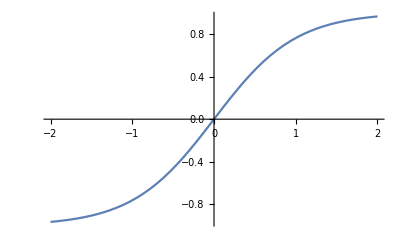

```mathematica
Plot[Tanh[x],{x,-2,2}]
```